```mathematica
GeoGraphics[GeoStyling["StreetMapNoLabels"], GeoRange->{{42.2,42.8},{1.4,2.1}}]
```

-Graphics-

```mathematica
GeoGraphics[GeoStyling["OutlineMap"],GeoRange->{{42.2,42.8},{1.2,2.3}},GeoScaleBar->{"Metric","Imperial"}]
```

-Graphics-

GeoGraphics::missloc: Unable to obtain location information for Melilla, Spain.

GeoGraphics::missloc: Unable to obtain location information for Ceuta, Spain.

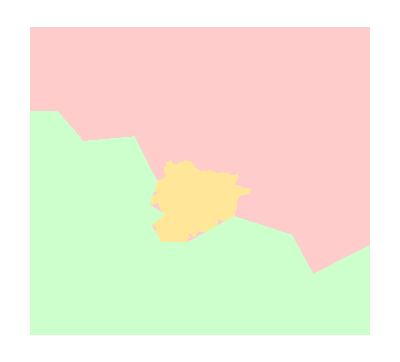

```mathematica
GeoGraphics[{GeoStyling[RGBColor[1,.8,.8], Opacity[1]],Polygon[LinguisticAssistant ], GeoStyling[RGBColor[1,.9,.6], Opacity[1]], Polygon[LinguisticAssistant], GeoStyling[RGBColor[.8,1,.8], Opacity[1]], Polygon[LinguisticAssistant]}, GeoRange->{{42.2,43},{1.0,2.2}}, GeoBackground->RGBColor[.7, .9,1]]
```

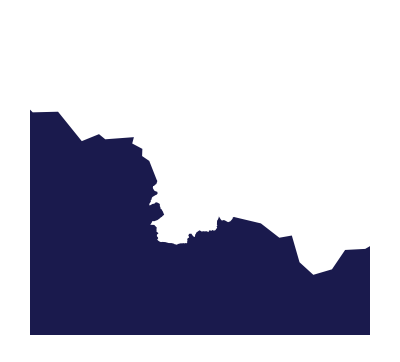

```mathematica
GeoGraphics[{GeoStyling[RGBColor[0.1,0.1,0.3],Opacity[1]],CountryData["Spain"]["Polygon"]},GeoRange->{{42.2,43},{1.0,2.2}},GeoBackground->None]
```

```mathematica
EntityClass["Country", "Spain"]
```

EntityClass[Country,Spain]

```mathematica
"plot in world map""country group"Manipulate[Graphics[({If[CountryData[#1,cl],Directive[Orange,EdgeForm[Brown]],LightBrown],Tooltip[CountryData[#1,{"SchematicPolygon","Robinson"}],{CountryData[#1,"Name"],CountryData[#1,prop]}]}&)/@CanonicalName[CountryData[]],ImageSize->500],{{cl,"Spain","country group"},Dynamic[CanonicalName[CountryData["Classes"]],SynchronousUpdating->False],ControlType->PopupMenu},{{prop,"Population","country property"},Dynamic[CountryData["Properties"],SynchronousUpdating->False],ControlType->PopupMenu},SynchronousUpdating->False]
```

CountryData::notprop: "Spain" is not a known property for CountryData. Use CountryData["Properties"] for a list of properties.

General::stop: Further output of CountryData::notprop will be suppressed during this calculation.

CountryData::notprop: "Spain" is not a known property for CountryData. Use CountryData["Properties"] for a list of properties.

General::stop: Further output of CountryData::notprop will be suppressed during this calculation.

CountryData::notprop: "Spain" is not a known property for CountryData. Use CountryData["Properties"] for a list of properties.

General::stop: Further output of CountryData::notprop will be suppressed during this calculation.

CountryData::notprop: "Spain" is not a known property for CountryData. Use CountryData["Properties"] for a list of properties.

General::stop: Further output of CountryData::notprop will be suppressed during this calculation.

CountryData::notprop: "Spain" is not a known property for CountryData. Use CountryData["Properties"] for a list of properties.

General::stop: Further output of CountryData::notprop will be suppressed during this calculation.

```mathematica
CountryData["Spain"]["Polygon"]
```

Polygon[GeoPosition[…]]